```mathematica
PacletInstall["Wolfram/QuantumFramework"]
Needs["Wolfram`QuantumFramework`"]
```

PacletObject[…]

```mathematica
qb=(QuantumState["0"]+QuantumState["1"])/Sqrt[2];

qb//TraditionalForm

qs=qb QuantumState["01"];
qs//TraditionalForm
```

1/(√2)0+1/(√2)1

Failure[…]

```mathematica
QuantumState[{α,β},2]//TraditionalForm
QuantumState[{α,β},2]//TraditionalForm
```

α0+β1

α0+β1

000

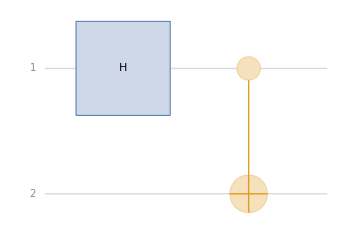

1/(√2)000+1/(√2)110

```mathematica
qs=(QuantumState["000"]);
TraditionalForm[qs]
qc=QuantumCircuitOperator[List[
	QuantumOperator["H",{1}],
	QuantumOperator["C",{1,2}]
	(*QuantumOperator["H",{2}],
	QuantumOperator["CX",{2,3}],
	QuantumOperator["CX",{1,2}],
	QuantumOperator["H",{1}]*)
]];
qc["Diagram"]
qc[qs]//TraditionalForm
```

```mathematica
QuantumOperator["RX"[t]]["Formula"]
```

Cos[t/2]00-ⅈ Sin[t/2]01-ⅈ Sin[t/2]10+Cos[t/2]11

000

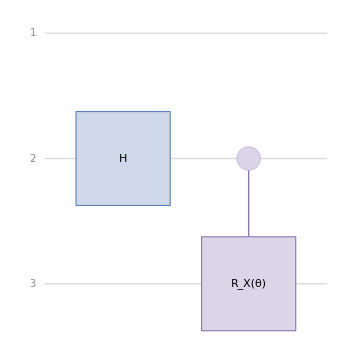

1/(√2)000+(cos(θ/2))/(√2)010-(ⅈ sin(θ/2))/(√2)011

```mathematica
qs=(QuantumState["000"]);
TraditionalForm[qs]
qc=QuantumCircuitOperator[List[
	QuantumOperator["H",{2}],
	QuantumOperator[{"C","RX"[θ]->{3},{2}}]
]];
qc["Diagram"]
qc[qs]//TraditionalForm
```

000

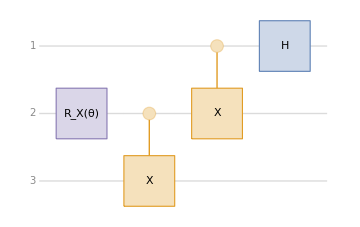

(cos(θ/2))/(√2)000-(ⅈ sin(θ/2))/(√2)011+(cos(θ/2))/(√2)100-(ⅈ sin(θ/2))/(√2)111

```mathematica
qs=(QuantumState["000"]);
TraditionalForm[qs]
qc=QuantumCircuitOperator[List[
	QuantumOperator["RX"[θ],{2}],
	QuantumOperator["CX",{2,3}],
	QuantumOperator["CX",{1,2}],
	QuantumOperator["H",{1}]
]];
qc["Diagram"]
qc[qs]//TraditionalForm
```

000

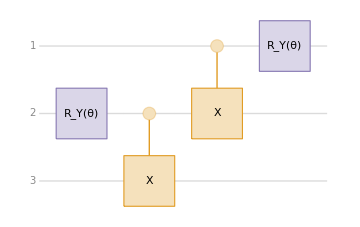

cos^2(θ/2)000+sin(θ/2) cos(θ/2)011+sin(θ/2) cos(θ/2)100+sin^2(θ/2)111

```mathematica
qs=(QuantumState["000"]);
TraditionalForm[qs]
qc=QuantumCircuitOperator[List[
	QuantumOperator["RY"[θ],{2}],
	QuantumOperator["CX",{2,3}],
	QuantumOperator["CX",{1,2}],
	QuantumOperator["RY"[θ],{1}]
]];
qc["Diagram"]
qc[qs]//TraditionalForm
```

```mathematica
QuantumMeasurement
```

```mathematica
qs=(QuantumState["000"]);
TraditionalForm[qs]
qc=QuantumCircuitOperator[List[
	QuantumOperator["RY"[θ],{2}],
	QuantumOperator["CX",{2,3}],
	QuantumOperator["CX",{1,2}],
	QuantumOperator["RY"[θ],{1}]
]];
qc["Diagram"]
qc[qs]//TraditionalForm
```

000

-Graphics-

cos^2(θ/2)000+sin(θ/2) cos(θ/2)011+sin(θ/2) cos(θ/2)100+sin^2(θ/2)111

```mathematica
qs2=QuantumMeasurementOperator["Z"][qc[qs]]
qs2["States"]//TraditionalForm
```

QuantumMeasurement[…]

{cos^2(θ/2)𝓏_+00+cos(θ/2) sin(θ/2)𝓏_+11,cos(θ/2) sin(θ/2)𝓏_−00+sin^2(θ/2)𝓏_−11}

000

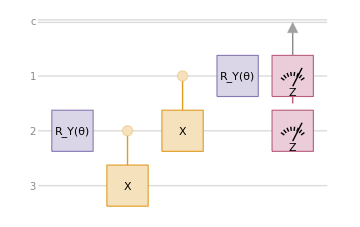

<|𝓏_+𝓏_+→Abs[Cos[θ/2]^2 Cos[Conjugate[θ]/2]^2]/(Abs[Cos[θ/2]^2 Cos[Conjugate[θ]/2]^2]+2 Abs[Cos[θ/2] Cos[Conjugate[θ]/2] Sin[θ/2] Sin[Conjugate[θ]/2]]+Abs[Sin[θ/2]^2 Sin[Conjugate[θ]/2]^2]),𝓏_+𝓏_−→Abs[Cos[θ/2] Cos[Conjugate[θ]/2] Sin[θ/2] Sin[Conjugate[θ]/2]]/(Abs[Cos[θ/2]^2 Cos[Conjugate[θ]/2]^2]+2 Abs[Cos[θ/2] Cos[Conjugate[θ]/2] Sin[θ/2] Sin[Conjugate[θ]/2]]+Abs[Sin[θ/2]^2 Sin[Conjugate[θ]/2]^2]),𝓏_−𝓏_+→Abs[Cos[θ/2] Cos[Conjugate[θ]/2] Sin[θ/2] Sin[Conjugate[θ]/2]]/(Abs[Cos[θ/2]^2 Cos[Conjugate[θ]/2]^2]+2 Abs[Cos[θ/2] Cos[Conjugate[θ]/2] Sin[θ/2] Sin[Conjugate[θ]/2]]+Abs[Sin[θ/2]^2 Sin[Conjugate[θ]/2]^2]),𝓏_−𝓏_−→Abs[Sin[θ/2]^2 Sin[Conjugate[θ]/2]^2]/(Abs[Cos[θ/2]^2 Cos[Conjugate[θ]/2]^2]+2 Abs[Cos[θ/2] Cos[Conjugate[θ]/2] Sin[θ/2] Sin[Conjugate[θ]/2]]+Abs[Sin[θ/2]^2 Sin[Conjugate[θ]/2]^2])|>

```mathematica
qs=(QuantumState["000"]);
TraditionalForm[qs]
qc=QuantumCircuitOperator[List[
	QuantumOperator["RY"[θ],{2}],
	QuantumOperator["CX",{2,3}],
	QuantumOperator["CX",{1,2}],
	QuantumOperator["RY"[θ],{1}],
	QuantumMeasurementOperator["Z",{1,2}]
]];
qc["Diagram"]
qc[qs]//TraditionalForm
```

000

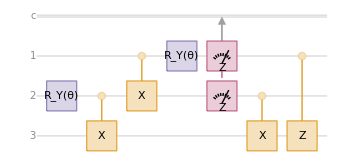

<|00→Abs[Cos[θ/2]^2 Cos[Conjugate[θ]/2]^2]/(Abs[Cos[θ/2]^2 Cos[Conjugate[θ]/2]^2]+2 Abs[Cos[θ/2] Cos[Conjugate[θ]/2] Sin[θ/2] Sin[Conjugate[θ]/2]]+Abs[Sin[θ/2]^2 Sin[Conjugate[θ]/2]^2]),01→Abs[Cos[θ/2] Cos[Conjugate[θ]/2] Sin[θ/2] Sin[Conjugate[θ]/2]]/(Abs[Cos[θ/2]^2 Cos[Conjugate[θ]/2]^2]+2 Abs[Cos[θ/2] Cos[Conjugate[θ]/2] Sin[θ/2] Sin[Conjugate[θ]/2]]+Abs[Sin[θ/2]^2 Sin[Conjugate[θ]/2]^2]),10→Abs[Cos[θ/2] Cos[Conjugate[θ]/2] Sin[θ/2] Sin[Conjugate[θ]/2]]/(Abs[Cos[θ/2]^2 Cos[Conjugate[θ]/2]^2]+2 Abs[Cos[θ/2] Cos[Conjugate[θ]/2] Sin[θ/2] Sin[Conjugate[θ]/2]]+Abs[Sin[θ/2]^2 Sin[Conjugate[θ]/2]^2]),11→Abs[Sin[θ/2]^2 Sin[Conjugate[θ]/2]^2]/(Abs[Cos[θ/2]^2 Cos[Conjugate[θ]/2]^2]+2 Abs[Cos[θ/2] Cos[Conjugate[θ]/2] Sin[θ/2] Sin[Conjugate[θ]/2]]+Abs[Sin[θ/2]^2 Sin[Conjugate[θ]/2]^2])|>

```mathematica
qs=(QuantumState["000"]);
TraditionalForm[qs]
qc=QuantumCircuitOperator[List[
	QuantumOperator["RY"[θ],{2}],
	QuantumOperator["CX",{2,3}],
	QuantumOperator["CX",{1,2}],
	QuantumOperator["RY"[θ],{1}],
	QuantumMeasurementOperator["Z",{1,2}],
	QuantumOperator["CX",{2,3}],
	QuantumOperator["CZ",{1,3}]
]];
qc["Diagram"]
qc[qs]//TraditionalForm
```

000

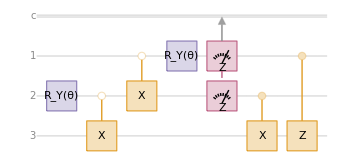

<|00→Abs[Cos[θ/2] Cos[Conjugate[θ]/2] Sin[θ/2] Sin[Conjugate[θ]/2]]/(Abs[Cos[θ/2]^2 Cos[Conjugate[θ]/2]^2]+2 Abs[Cos[θ/2] Cos[Conjugate[θ]/2] Sin[θ/2] Sin[Conjugate[θ]/2]]+Abs[Sin[θ/2]^2 Sin[Conjugate[θ]/2]^2]),01→Abs[Cos[θ/2]^2 Cos[Conjugate[θ]/2]^2]/(Abs[Cos[θ/2]^2 Cos[Conjugate[θ]/2]^2]+2 Abs[Cos[θ/2] Cos[Conjugate[θ]/2] Sin[θ/2] Sin[Conjugate[θ]/2]]+Abs[Sin[θ/2]^2 Sin[Conjugate[θ]/2]^2]),10→Abs[Sin[θ/2]^2 Sin[Conjugate[θ]/2]^2]/(Abs[Cos[θ/2]^2 Cos[Conjugate[θ]/2]^2]+2 Abs[Cos[θ/2] Cos[Conjugate[θ]/2] Sin[θ/2] Sin[Conjugate[θ]/2]]+Abs[Sin[θ/2]^2 Sin[Conjugate[θ]/2]^2]),11→Abs[Cos[θ/2] Cos[Conjugate[θ]/2] Sin[θ/2] Sin[Conjugate[θ]/2]]/(Abs[Cos[θ/2]^2 Cos[Conjugate[θ]/2]^2]+2 Abs[Cos[θ/2] Cos[Conjugate[θ]/2] Sin[θ/2] Sin[Conjugate[θ]/2]]+Abs[Sin[θ/2]^2 Sin[Conjugate[θ]/2]^2])|>

```mathematica
qs=(QuantumState["000"]);
TraditionalForm[qs]
qc=QuantumCircuitOperator[List[
	QuantumOperator["RY"[θ],{2}],
	QuantumOperator[{"C0","X"->3,{2}}],
	QuantumOperator[{"C0","X"->2,{1}}],
	QuantumOperator["RY"[θ],{1}],
	QuantumMeasurementOperator["Z",{1,2}],
	QuantumOperator["CX",{2,3}],
	QuantumOperator["CZ",{1,3}]
]];
qc["Diagram"]
qc[qs]//TraditionalForm
```

## The actual teleportation protocol

```mathematica
(α QuantumState["001"] + β QuantumState["101"])["Formula"]
```

α001+β101

```mathematica
(QuantumState[{0,0,α,β},2])["Formula"]
```

α10+β11

```mathematica
(QuantumState["UniformSuperposition"[α]])["Formula"]
(QuantumState[{α,β}])["Formula"]
QuantumState[{3,2,ⅈ 5,1},{2,2}]["Formula"]
QuantumState[{3,2,ⅈ 5,1}]["Formula"]
QuantumState[{0,0,0,0,0,1}]["Formula"]
QuantumState[{1,0,0,0,1},{3,3}]["Formula"]
QuantumState[{{α,β},0},2]["Formula"]
```

UniformSuperposition0+α1

α0+β1

300+201+5 ⅈ10+11

300+201+5 ⅈ10+11

12

00+11

$IterationLimit::itlim: Iteration limit of 4096 exceeded.

TerminatedEvaluation[IterationLimit][Formula]

α001+β101

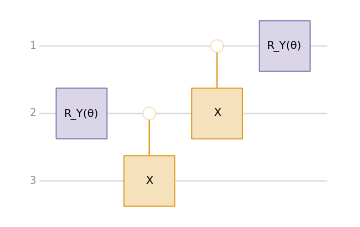

QuantumState[…]

-β sin(θ/2) cos(θ/2)000+α sin(θ/2) cos(θ/2)001+α cos^2(θ/2)010-β sin^2(θ/2)011+β cos^2(θ/2)100+α sin^2(θ/2)101+α sin(θ/2) cos(θ/2)110+β sin(θ/2) cos(θ/2)111

QuantumState[…]

```mathematica
η=θ;
qs=(α QuantumState["001"] + β QuantumState["101"]);
TraditionalForm[qs]
qc=QuantumCircuitOperator[List[
	QuantumOperator["RY"[η],{2}],
	QuantumOperator[{"C0","X"->3,{2}}],
	QuantumOperator[{"C0","X"->2,{1}}],
	QuantumOperator["RY"[η],{1}](*,
	QuantumMeasurementOperator["Z",{1,2}],
	QuantumOperator["CX",{2,3}],
	QuantumOperator["CZ",{1,3}]*)
]];
qc["Diagram"]
result=qc[qs]
result//TraditionalForm
result[qs]//StandardForm
```

α001+β101

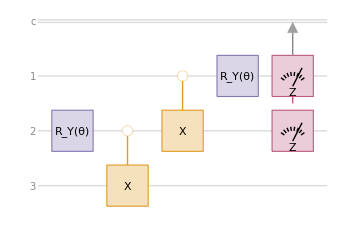

QuantumMeasurement[…]

<|𝓏_+𝓏_+→Abs[α Conjugate[α] Cos[θ/2] Cos[Conjugate[θ]/2] Sin[θ/2] Sin[Conjugate[θ]/2]+β Conjugate[β] Cos[θ/2] Cos[Conjugate[θ]/2] Sin[θ/2] Sin[Conjugate[θ]/2]]/(2 Abs[α Conjugate[α] Cos[θ/2] Cos[Conjugate[θ]/2] Sin[θ/2] Sin[Conjugate[θ]/2]+β Conjugate[β] Cos[θ/2] Cos[Conjugate[θ]/2] Sin[θ/2] Sin[Conjugate[θ]/2]]+Abs[β Conjugate[β] Cos[θ/2]^2 Cos[Conjugate[θ]/2]^2+α Conjugate[α] Sin[θ/2]^2 Sin[Conjugate[θ]/2]^2]+Abs[α Conjugate[α] Cos[θ/2]^2 Cos[Conjugate[θ]/2]^2+β Conjugate[β] Sin[θ/2]^2 Sin[Conjugate[θ]/2]^2]),𝓏_+𝓏_−→Abs[α Conjugate[α] Cos[θ/2]^2 Cos[Conjugate[θ]/2]^2+β Conjugate[β] Sin[θ/2]^2 Sin[Conjugate[θ]/2]^2]/(2 Abs[α Conjugate[α] Cos[θ/2] Cos[Conjugate[θ]/2] Sin[θ/2] Sin[Conjugate[θ]/2]+β Conjugate[β] Cos[θ/2] Cos[Conjugate[θ]/2] Sin[θ/2] Sin[Conjugate[θ]/2]]+Abs[β Conjugate[β] Cos[θ/2]^2 Cos[Conjugate[θ]/2]^2+α Conjugate[α] Sin[θ/2]^2 Sin[Conjugate[θ]/2]^2]+Abs[α Conjugate[α] Cos[θ/2]^2 Cos[Conjugate[θ]/2]^2+β Conjugate[β] Sin[θ/2]^2 Sin[Conjugate[θ]/2]^2]),𝓏_−𝓏_+→Abs[β Conjugate[β] Cos[θ/2]^2 Cos[Conjugate[θ]/2]^2+α Conjugate[α] Sin[θ/2]^2 Sin[Conjugate[θ]/2]^2]/(2 Abs[α Conjugate[α] Cos[θ/2] Cos[Conjugate[θ]/2] Sin[θ/2] Sin[Conjugate[θ]/2]+β Conjugate[β] Cos[θ/2] Cos[Conjugate[θ]/2] Sin[θ/2] Sin[Conjugate[θ]/2]]+Abs[β Conjugate[β] Cos[θ/2]^2 Cos[Conjugate[θ]/2]^2+α Conjugate[α] Sin[θ/2]^2 Sin[Conjugate[θ]/2]^2]+Abs[α Conjugate[α] Cos[θ/2]^2 Cos[Conjugate[θ]/2]^2+β Conjugate[β] Sin[θ/2]^2 Sin[Conjugate[θ]/2]^2]),𝓏_−𝓏_−→Abs[α Conjugate[α] Cos[θ/2] Cos[Conjugate[θ]/2] Sin[θ/2] Sin[Conjugate[θ]/2]+β Conjugate[β] Cos[θ/2] Cos[Conjugate[θ]/2] Sin[θ/2] Sin[Conjugate[θ]/2]]/(2 Abs[α Conjugate[α] Cos[θ/2] Cos[Conjugate[θ]/2] Sin[θ/2] Sin[Conjugate[θ]/2]+β Conjugate[β] Cos[θ/2] Cos[Conjugate[θ]/2] Sin[θ/2] Sin[Conjugate[θ]/2]]+Abs[β Conjugate[β] Cos[θ/2]^2 Cos[Conjugate[θ]/2]^2+α Conjugate[α] Sin[θ/2]^2 Sin[Conjugate[θ]/2]^2]+Abs[α Conjugate[α] Cos[θ/2]^2 Cos[Conjugate[θ]/2]^2+β Conjugate[β] Sin[θ/2]^2 Sin[Conjugate[θ]/2]^2])|>

QuantumMeasurement[…][QuantumState[…]]

```mathematica
η=θ;
qs=(α QuantumState["001"] + β QuantumState["101"]);
TraditionalForm[qs]
qc=QuantumCircuitOperator[List[
	QuantumOperator["RY"[η],{2}],
	QuantumOperator[{"C0","X"->3,{2}}],
	QuantumOperator[{"C0","X"->2,{1}}],
	QuantumOperator["RY"[η],{1}],
	QuantumMeasurementOperator["Z",{1,2}](*,
	QuantumOperator["CX",{2,3}],
	QuantumOperator["CZ",{1,3}]*)
]];
qc["Diagram"]
result=qc[qs]
result//TraditionalForm
result[qs]//StandardForm
```

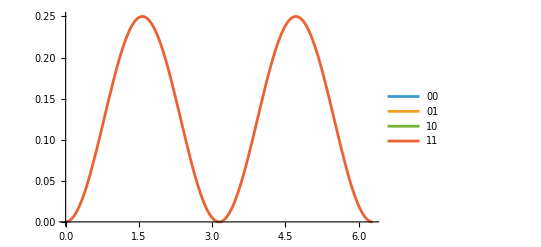

-Graphics-

-Graphics-

```mathematica
result["Probabilities"];
valRes=Values[result["Probabilities"]];
Plot[{valRes[[1]]/.θ->x,valRes[[2]]/.θ->x,valRes[[3]]/.θ->x,valRes[[4]]/.{θ->x,α->1,β->1}},{x,0,2Pi},PlotLegends->{"00","01","10","11"}]
Plot[{valRes[[1]]/.θ->x,valRes[[2]]/.θ->x,valRes[[3]]/.θ->x,valRes[[4]]/.{θ->x,α->1,β->0}},{x,0,2Pi},PlotLegends->{"00","01","10","11"}]
Plot[{valRes[[1]]/.θ->x,valRes[[2]]/.θ->x,valRes[[3]]/.θ->x,valRes[[4]]/.{θ->x,α->0,β->1}},{x,0,2Pi},PlotLegends->{"00","01","10","11"}]
```

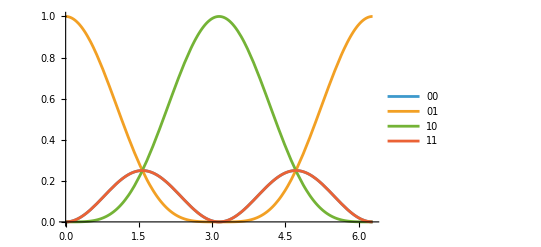

```mathematica
Plot[{valRes[[1]]/.θ->x,valRes[[2]]/.θ->x,valRes[[3]]/.θ->x,valRes[[4]]/.θ->x},{x,0,2Pi},PlotLegends->{"00","01","10","11"}]
```

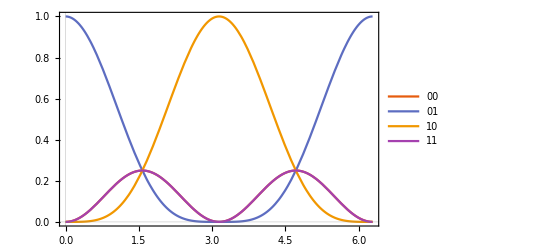

```mathematica
graph=Plot[{valRes⟦1⟧/.θ->x,valRes⟦2⟧/.θ->x,valRes⟦3⟧/.θ->x,valRes⟦4⟧/.θ->x},{x,0,2 π},PlotTheme->"Scientific",PlotLegends->{"00","01","10","11"}]
```

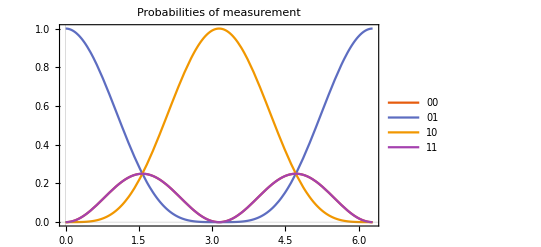

```mathematica
Show[graph,PlotLabel->HoldForm[Probabilities of measurement],LabelStyle->{20,GrayLevel[0]}]
```

```mathematica
Export["/home/frenour/Documents/GitRepos/NanoTech-Masters/classNotes/4_QuantumComputation/hmksMarco/Challenge/probabilities.png",%248,"PNG"]
```

/home/frenour/Documents/GitRepos/NanoTech-Masters/classNotes/4_QuantumComputation/hmksMarco/Challenge/probabilities.png

```mathematica
Show[%240,AspectRatio->1/GoldenRatio]
```

-Graphics-

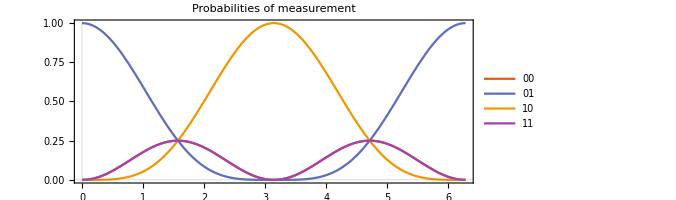

```mathematica
Show[%240,AspectRatio->Full]
```

```mathematica
Show[%240,AspectRatio->Automatic]
```

-Graphics-

### Miau

α001+β101

-Graphics-

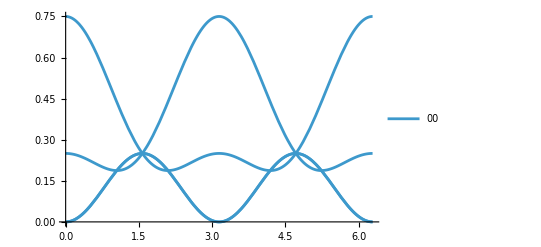

```mathematica
η=θ;
qs=(α QuantumState["001"] + β QuantumState["101"]);
TraditionalForm[qs]
qc=QuantumCircuitOperator[List[
	QuantumOperator["RY"[η],{2}],
	QuantumOperator[{"C0","X"->3,{2}}],
	QuantumOperator[{"C0","X"->2,{1}}],
	QuantumOperator["RY"[η],{1}],
	QuantumMeasurementOperator["Z",{1,2}](*,
	QuantumOperator["CX",{2,3}],
	QuantumOperator["CZ",{1,3}]*)
]];
qc["Diagram"]
result=qc[qs];
result//TraditionalForm;
result[qs]//StandardForm;
result["Probabilities"];
valRes=Values[result["Probabilities"]];
Plot[({valRes[[1]]/.{θ->x,β->Sqrt[1-α^2]},valRes[[2]]/.{θ->x,β->Sqrt[1-α^2]},valRes[[3]]/.{θ->x,β->Sqrt[1-α^2]},valRes[[4]]/.{θ->x,β->Sqrt[1-α^2]}})/.α->0.5,{x,0,2Pi},PlotLegends->{"00","01","10","11"}]
```

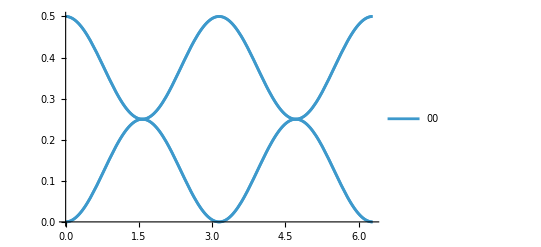

```mathematica
Plot[{valRes[[1]]/.θ->x,valRes[[2]]/.θ->x,valRes[[3]]/.θ->x,valRes[[4]]/.{θ->x}}/.{θ->x,α->1,β->1},{x,0,2Pi},PlotLegends->{"00","01","10","11"}]
Plot[{valRes[[1]]/.θ->x,valRes[[2]]/.θ->x,valRes[[3]]/.θ->x,valRes[[4]]/.{θ->x}}/.{θ->x,α->1,β->1},{x,0,2Pi},PlotLegends->{"00","01","10","11"}]
```

### Miau 2

α001

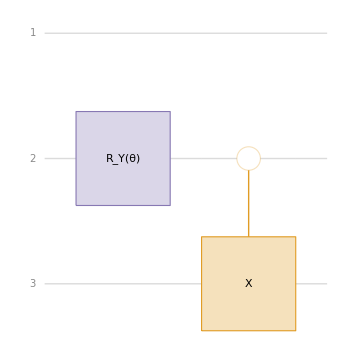

α cos(θ/2)000+α sin(θ/2)011

```mathematica
η=θ;
qs=(α QuantumState["001"] + 0 QuantumState["101"]);
TraditionalForm[qs]
qc=QuantumCircuitOperator[List[
	QuantumOperator["RY"[η],{2}],
	QuantumOperator[{"C0","X"->3,{2}}]
]];
qc["Diagram"]
result=qc[qs];
result//TraditionalForm
result[qs]//StandardForm;
```

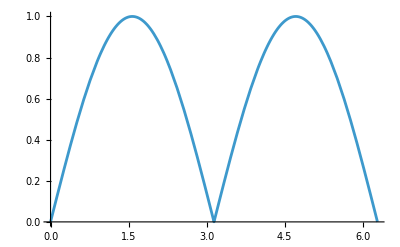

```mathematica
Plot[Abs[Sin[x]],{x,0,2π}]
```

### The recipies for I don’t know

#### Case 1

000

-Graphics-

QuantumMeasurement[…]

<|00→Abs[Cos[θ/2] Cos[Conjugate[θ]/2] Sin[θ/2] Sin[Conjugate[θ]/2]]/(Abs[Cos[θ/2]^2 Cos[Conjugate[θ]/2]^2]+2 Abs[Cos[θ/2] Cos[Conjugate[θ]/2] Sin[θ/2] Sin[Conjugate[θ]/2]]+Abs[Sin[θ/2]^2 Sin[Conjugate[θ]/2]^2]),01→Abs[Cos[θ/2]^2 Cos[Conjugate[θ]/2]^2]/(Abs[Cos[θ/2]^2 Cos[Conjugate[θ]/2]^2]+2 Abs[Cos[θ/2] Cos[Conjugate[θ]/2] Sin[θ/2] Sin[Conjugate[θ]/2]]+Abs[Sin[θ/2]^2 Sin[Conjugate[θ]/2]^2]),10→Abs[Sin[θ/2]^2 Sin[Conjugate[θ]/2]^2]/(Abs[Cos[θ/2]^2 Cos[Conjugate[θ]/2]^2]+2 Abs[Cos[θ/2] Cos[Conjugate[θ]/2] Sin[θ/2] Sin[Conjugate[θ]/2]]+Abs[Sin[θ/2]^2 Sin[Conjugate[θ]/2]^2]),11→Abs[Cos[θ/2] Cos[Conjugate[θ]/2] Sin[θ/2] Sin[Conjugate[θ]/2]]/(Abs[Cos[θ/2]^2 Cos[Conjugate[θ]/2]^2]+2 Abs[Cos[θ/2] Cos[Conjugate[θ]/2] Sin[θ/2] Sin[Conjugate[θ]/2]]+Abs[Sin[θ/2]^2 Sin[Conjugate[θ]/2]^2])|>

QuantumMeasurement[…][QuantumState[…]]

{Abs[Cos[θ/2] Cos[Conjugate[θ]/2] Sin[θ/2] Sin[Conjugate[θ]/2]]/(Abs[Cos[θ/2]^2 Cos[Conjugate[θ]/2]^2]+2 Abs[Cos[θ/2] Cos[Conjugate[θ]/2] Sin[θ/2] Sin[Conjugate[θ]/2]]+Abs[Sin[θ/2]^2 Sin[Conjugate[θ]/2]^2]),Abs[Cos[θ/2]^2 Cos[Conjugate[θ]/2]^2]/(Abs[Cos[θ/2]^2 Cos[Conjugate[θ]/2]^2]+2 Abs[Cos[θ/2] Cos[Conjugate[θ]/2] Sin[θ/2] Sin[Conjugate[θ]/2]]+Abs[Sin[θ/2]^2 Sin[Conjugate[θ]/2]^2]),Abs[Sin[θ/2]^2 Sin[Conjugate[θ]/2]^2]/(Abs[Cos[θ/2]^2 Cos[Conjugate[θ]/2]^2]+2 Abs[Cos[θ/2] Cos[Conjugate[θ]/2] Sin[θ/2] Sin[Conjugate[θ]/2]]+Abs[Sin[θ/2]^2 Sin[Conjugate[θ]/2]^2]),Abs[Cos[θ/2] Cos[Conjugate[θ]/2] Sin[θ/2] Sin[Conjugate[θ]/2]]/(Abs[Cos[θ/2]^2 Cos[Conjugate[θ]/2]^2]+2 Abs[Cos[θ/2] Cos[Conjugate[θ]/2] Sin[θ/2] Sin[Conjugate[θ]/2]]+Abs[Sin[θ/2]^2 Sin[Conjugate[θ]/2]^2])}

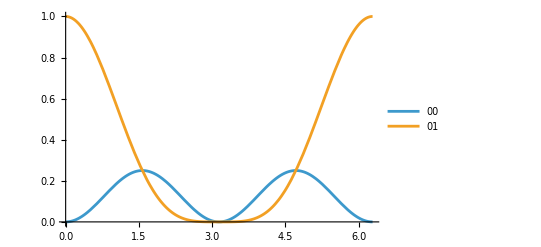

-Graphics-

```mathematica
η=θ;
qs=(QuantumState["000"]);
TraditionalForm[qs]
qc=QuantumCircuitOperator[List[
	QuantumOperator["RY"[η],{2}],
	QuantumOperator[{"C0","X"->3,{2}}],
	QuantumOperator[{"C0","X"->2,{1}}],
	QuantumOperator["RY"[η],{1}],
	QuantumMeasurementOperator["Z",{1,2}],
	QuantumOperator["CX",{2,3}],
	QuantumOperator["CZ",{1,3}]
]];
qc["Diagram"]
result=qc[qs]
result//TraditionalForm
result[qs]//StandardForm
result["Probabilities"];
valRes=Values[result["Probabilities"]]
Plot[{valRes[[1]]/.θ->x,valRes[[2]]/.θ->x},{x,0,2Pi},PlotLegends->{"00","01"}]

Plot[{valRes[[1]]/.θ->x,valRes[[2]]/.θ->x,valRes[[3]]/.θ->x,valRes[[4]]/.θ->x},{x,0,2Pi},PlotLegends->{"00","01","10","11"}]
```

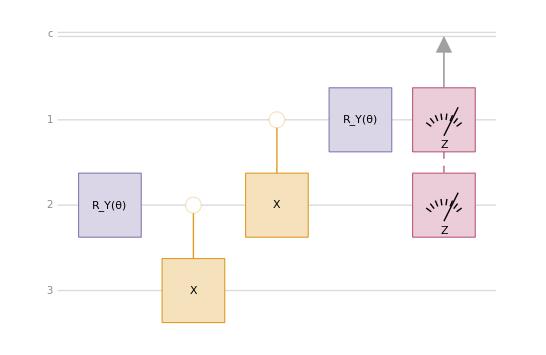

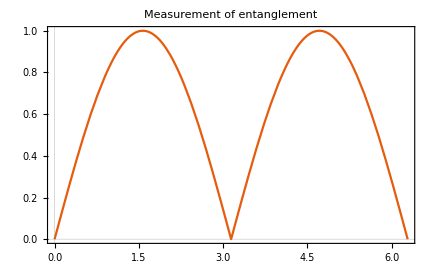

```mathematica
Plot[Abs[Sin[x]],{x,0,2π},PlotTheme->"Scientific",PlotLabel->HoldForm[Measurement of entanglement],LabelStyle->{20,GrayLevel[0]}]
```

```mathematica
Export["/home/frenour/Documents/GitRepos/NanoTech-Masters/classNotes/4_QuantumComputation/hmksMarco/lastHmk/imgs/entanglement.png",%36,"PNG"]
```

/home/frenour/Documents/GitRepos/NanoTech-Masters/classNotes/4_QuantumComputation/hmksMarco/lastHmk/imgs/entanglement.png